# 2D Tiling

## Used and explained in the article “On the K-theory of C^*-algebras for substitution tilings (a pedestrian version)” by Daniel Gonçalves and Maria Ramirez-Solano.

## 1.Definition of prototiles and substitution of prototiles (user input)

```mathematica
(*prototile = a polygon with a corner at the origin  = list of points in the plane, called locations, which represent the corners of the polygon, listed in counterclockwise order, starting at the origin*)
tableCorners={{0,0},{1,0},{1,1},{0,1}};
p1=tableCorners;
prototiles={p1,p1,p1,p1};

(*inflation factor*)
λ=2;

(* tile = (prototilenumber, location) *)
(* tEdge = (tilenumber, edgenumber in the prototile) *)
(* tVertex = (tilenumber, vertexnumber in the prototile)  *)
(* protoEdge = (prototilenumber, edgenumber in the prototile) *)
(* protoVertex = (prototilenumber, vertexnumber in the prototile)  *)
(* wp0 = {(prototilenumber, location),(prototilenumber, location)... } = list of tiles*)
wp1={{3,{0,0}},{1,{1,0}},{1,{1,1}},{4,{0,1}}}; 
wp2={{2,{0,0}},{3,{1,0}},{4,{1,1}},{2,{0,1}}}; 
wp3={{1,{0,0}},{2,{1,0}},{3,{1,1}},{3,{0,1}}}; 
wp4={{4,{0,0}},{4,{1,0}},{2,{1,1}},{1,{0,1}}}; 
wPrototile={wp1,wp2,wp3,wp4};


MAXDegreeOfBoundaryVertices=1;(*USUALLY 1*)

(*auxiliary functions for constructing prototiles*)
rotation90=Function[location,{-location⟦2⟧,location⟦1⟧}];
rotation180=Function[location,-location];
rotation270=Function[location,{location⟦2⟧,-location⟦1⟧}];

centerOfMass=Function[locs,Apply[Plus,locs]/Length[locs]];
centerOfMassNearFirstVertex=Function[locs,locs⟦1⟧+.2(centerOfMass[locs]-locs⟦1⟧)];
wPrototileNumbers=Table[Map[#⟦1⟧&,wPrototile⟦i⟧],{i,1,Length[wPrototile]}]
drawwPrototile=Function[pNum,Module[{tnumbers,pnumbers,lcs},
lcs=Map[centerOfMassNearFirstVertex,ComputeLocations[wPrototile⟦pNum⟧]];tnumbers=Table[Text[i,lcs⟦i⟧],{i,1,Length[lcs]}];
pnumbers=Table[Text[wPrototileNumbers⟦pNum⟧⟦i⟧,lcs⟦i⟧],{i,1,Length[lcs]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦pNum⟧],Map[#⟦1⟧&,wPrototile⟦pNum⟧]],tnumbers}],
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦pNum⟧],Map[#⟦1⟧&,wPrototile⟦pNum⟧]],pnumbers}],"w(p_"<>ToString[pNum]<>")"}]];
drawPrototile=Function[
pNum,
Graphics[{polygonsColors[{prototiles⟦pNum⟧},{pNum}],Text[pNum,centerOfMassNearFirstVertex[prototiles⟦pNum⟧]]}]];
color=Join[{Red,RGBColor[.92,.26,.47],RGBColor[0,.71,.02],RGBColor[.35,.73,.51],Green,Cyan,Orange, Yellow,Blue,Purple,LightBlue,LightGray,LightGreen,Red,Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen},Table[RGBColor[(i/8+.5)/1.5,0,0],{i,1,8}],
Table[RGBColor[0,(i/8+.5)/1.5,0],{i,1,8}],
Table[RGBColor[0,0,(i/4+.5)/1.5],{i,1,4}]]
label={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z};

(* 
horonztal domino: p2|p4=b|d=green|greenish;
vertical domino:  p1/p3=a/c=red/redish 
colors and labels are modified for  this tiling!
*)
```

{{3,1,1,4},{2,3,4,2},{1,2,3,3},{4,4,2,1}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Map[Graphics[{Line[#],Point[#⟦1⟧]}]&,prototiles]*)
```

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

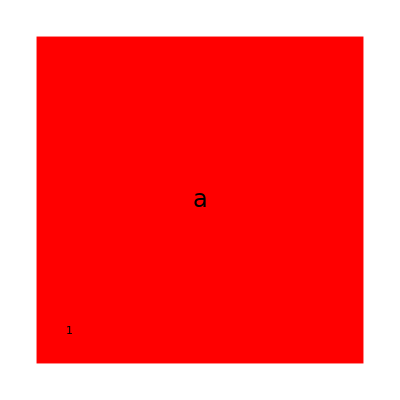
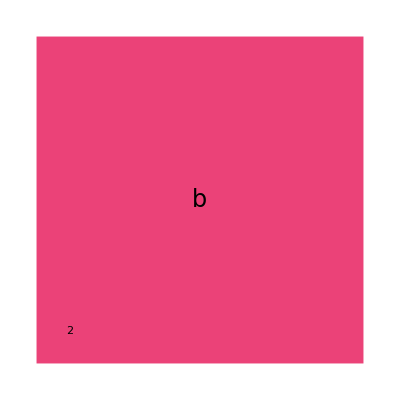
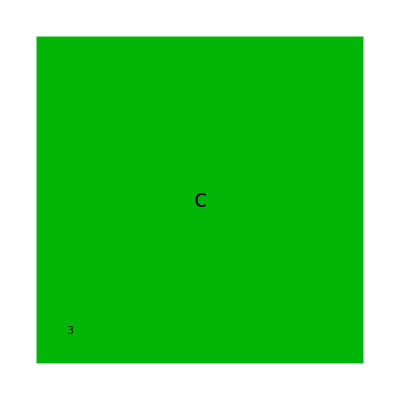
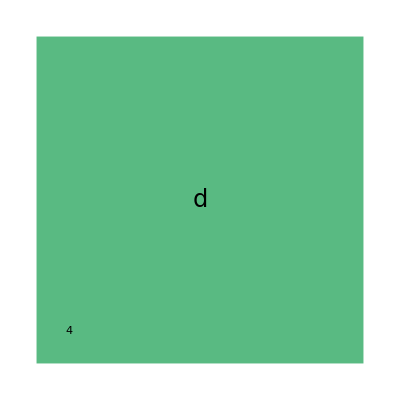

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]];
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]
polygonsLabels=Function[{polygonCorners,colorsIndices},Table[{
label⟦colorsIndices⟦i⟧⟧,Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]},
{i,1,Length[polygonCorners]}]];

Map[drawPrototile,Range[Length[prototiles]]]
```

```mathematica
Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]
```

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

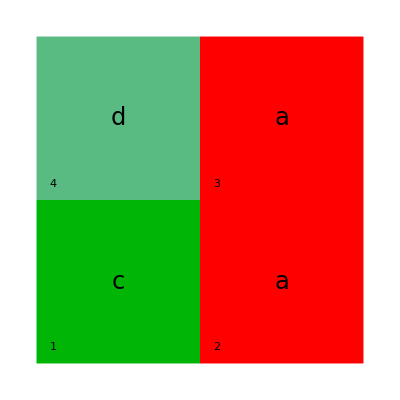
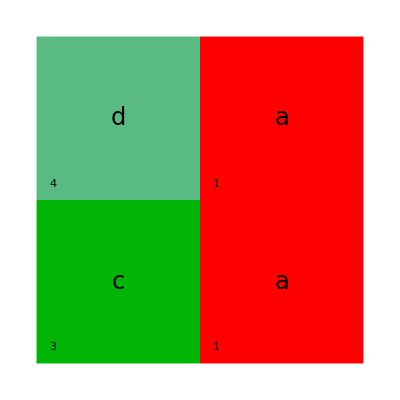
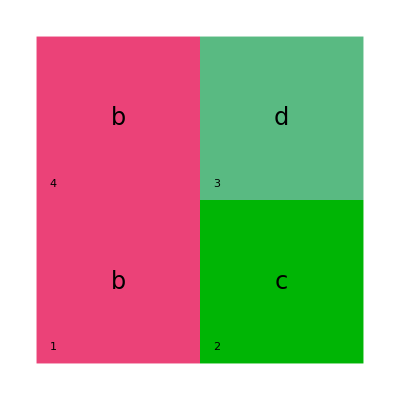
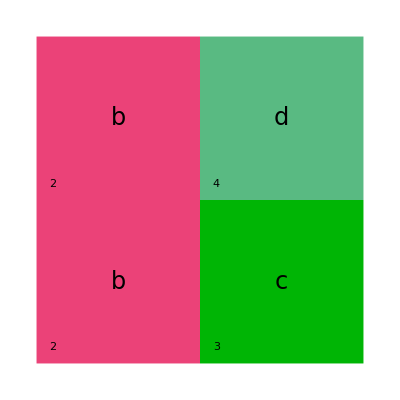
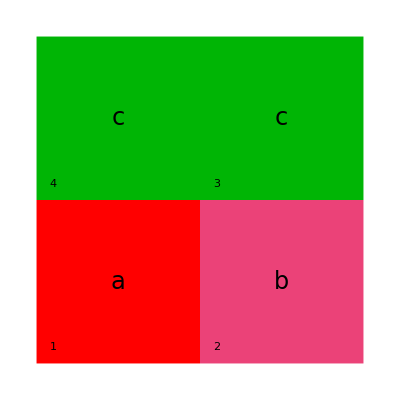
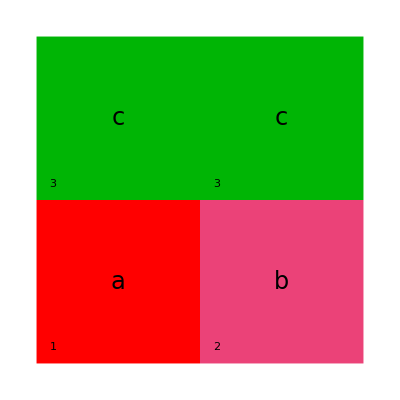
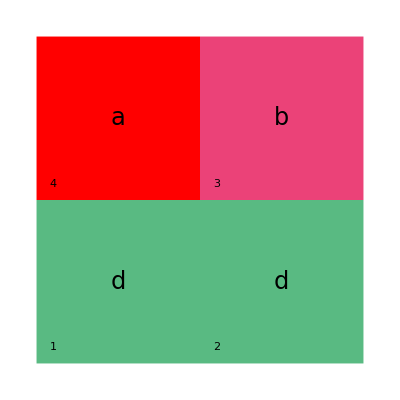
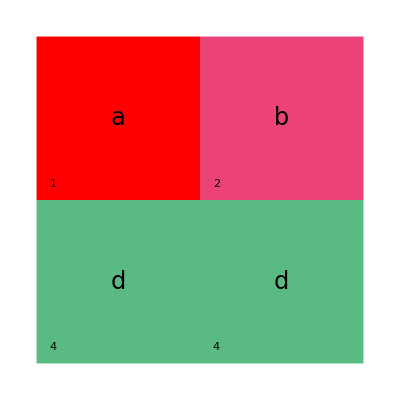
{{-Graphics-,-Graphics-,w(p_1)},{-Graphics-,-Graphics-,w(p_2)},{-Graphics-,-Graphics-,w(p_3)},{-Graphics-,-Graphics-,w(p_4)}}

```mathematica
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];


Map[drawwPrototile,Range[Length[prototiles]]]
```

## 2.Defining substitution ω(tiles) (run 1)

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColorsPlain=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]


(*ωTile(tile) = list of tiles which represent the substituted tile  *)
ωTile=Function[tile,Module[{tiles,prototileNumber,translation},
{prototileNumber,translation}=tile;
tiles=wPrototile⟦prototileNumber⟧;
(*tiles +λ translation*)
Table[{tiles⟦i⟧⟦1⟧,tiles⟦i⟧⟦2⟧+ λ translation},{i,1,Length[tiles]}]
]];
(*AddTranslation=Function[{locations,translation},Table[locations⟦i⟧+translation,{i,1,Length[locations]}]];*)
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];
(*ω substitutes a list of tiles by substituting each tile individually *)
ω=Function[tiles,Flatten[Map[ωTile,tiles],1]]
supertile=Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

(*maximum number smaller than the limit*)
bsearchMin[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list⟦m⟧==elem,While[list⟦m⟧==elem,m++];
Return[m-1]];
If[list⟦m⟧<elem,n0=m+1,n1=m-1]];
If[list⟦m⟧<elem,m,m-1]];

(*minimum number larger than the limit*)
bsearchMax[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[list[[m]]==elem,m--];
Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]];


varpepsilonZero=10^(-10);
positiveEdgeQ=Function[edgeLocation,Module[{x,y},{x,y}=edgeLocation⟦2⟧-edgeLocation⟦1⟧;If[x>0 || (Abs[x]<varpepsilonZero&&y>0),True,False]]];
(*computeEdgesDirections= {{1,1,1,-1,-1,,,},{1,1,-1,..}} where 1=samedirection, -1 opposite direction *)
computeEdgesDirections=Function[tileLocations,Module[{edge,lastedge},
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[positiveEdgeQ[edge]==True,1,-1],{i,1,Length[tileLocations]-1}],If[positiveEdgeQ[lastedge]==True,{1},{-1}]]]];
prototilesDirections=Map[computeEdgesDirections,prototiles]
prototilesLengths=Map[Length,prototiles]

Unflatten=Function[{list,lengths},Module[{k},
k=0;
Table[Table[k++;list⟦k⟧,{i,1,lengths⟦j⟧}],{j,1,Length[lengths]}]]];
swapVerticesofEdge=Function[v1v2,{v1v2⟦2⟧,v1v2⟦1⟧}];

cyclicRange=Function[{interval,n},Module[{a,b},
{a,b}=interval;
If[a≤ b,Range[a,b],
Join[Range[a,n],Range[b]]]]];
drawProtoEdge=Function[protoEdge,Module[{loc},
(*protoEdge={prototilenumber,number of edge on prototile} *)
loc=prototiles⟦protoEdge⟦1⟧⟧;
Graphics[{color⟦protoEdge⟦1⟧⟧,Polygon[loc], Black, Line[{loc⟦protoEdge⟦2⟧⟧,loc⟦Mod[protoEdge⟦2⟧+1,Length[loc],1]⟧}]}]]];
drawProtoVertex=Function[protoVertex,Module[{loc},loc=prototiles⟦protoVertex⟦1⟧⟧;Graphics[{color⟦protoVertex⟦1⟧⟧,Polygon[loc],Black,Point[{loc⟦protoVertex⟦2⟧⟧}]}]]];
```

Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[tiles,Flatten[ωTile/@tiles,1]]

Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

{{1,1,-1,-1},{1,1,-1,-1},{1,1,-1,-1},{1,1,-1,-1}}

{4,4,4,4}

4

4

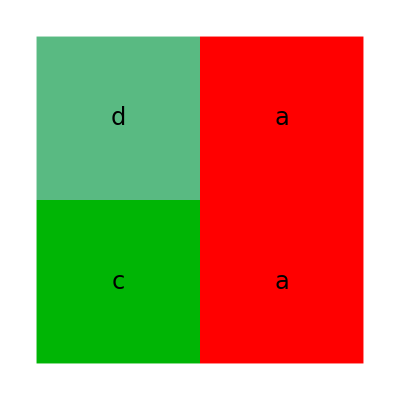
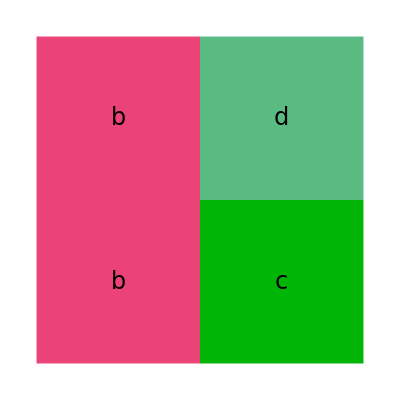
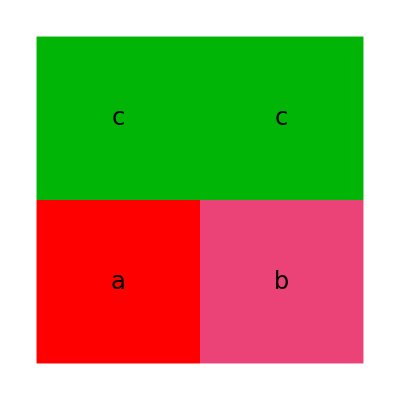
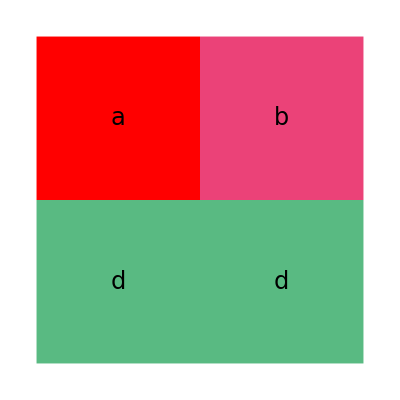

```mathematica
(*ω(prototiles)*)
prototiles//Length
(*ω(prototiles)*)
prototiles//Length
Table[Graphics[polygonsColors[ComputeLocations[ωTile[{i,{0,0}}]],Map[#⟦1⟧&,ωTile[{i,{0,0}}]]]],{i,1,Length[prototiles]}]
```

```mathematica
Expand[FullSimplify[supertile[1,3]]]
```

{{3,{0,0}},{1,{1,0}},{1,{1,1}},{4,{0,1}},{2,{2,0}},{3,{3,0}},{4,{3,1}},{2,{2,1}},{1,{2,2}},{2,{3,2}},{3,{3,3}},{3,{2,3}},{1,{0,2}},{2,{1,2}},{3,{1,3}},{3,{0,3}},{1,{4,0}},{2,{5,0}},{3,{5,1}},{3,{4,1}},{3,{6,0}},{1,{7,0}},{1,{7,1}},{4,{6,1}},{3,{6,2}},{1,{7,2}},{1,{7,3}},{4,{6,3}},{4,{4,2}},{4,{5,2}},{2,{5,3}},{1,{4,3}},{1,{4,4}},{2,{5,4}},{3,{5,5}},{3,{4,5}},{3,{6,4}},{1,{7,4}},{1,{7,5}},{4,{6,5}},{3,{6,6}},{1,{7,6}},{1,{7,7}},{4,{6,7}},{4,{4,6}},{4,{5,6}},{2,{5,7}},{1,{4,7}},{4,{0,4}},{4,{1,4}},{2,{1,5}},{1,{0,5}},{4,{2,4}},{4,{3,4}},{2,{3,5}},{1,{2,5}},{2,{2,6}},{3,{3,6}},{4,{3,7}},{2,{2,7}},{3,{0,6}},{1,{1,6}},{1,{1,7}},{4,{0,7}}}

```mathematica
Map[#[[1]]&,supertile[1,3]]
```

{3,1,1,4,2,3,4,2,1,2,3,3,1,2,3,3,1,2,3,3,3,1,1,4,3,1,1,4,4,4,2,1,1,2,3,3,3,1,1,4,3,1,1,4,4,4,2,1,4,4,2,1,4,4,2,1,2,3,4,2,3,1,1,4}

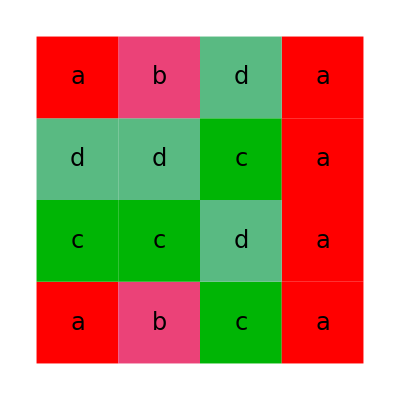

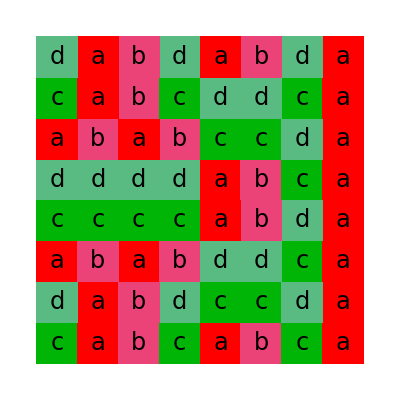

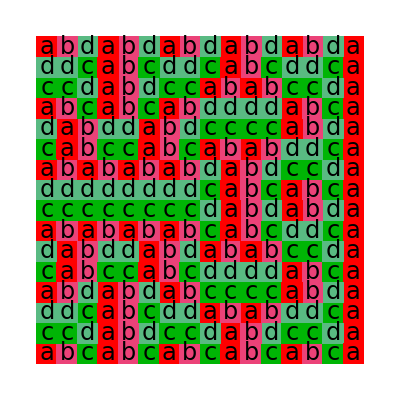

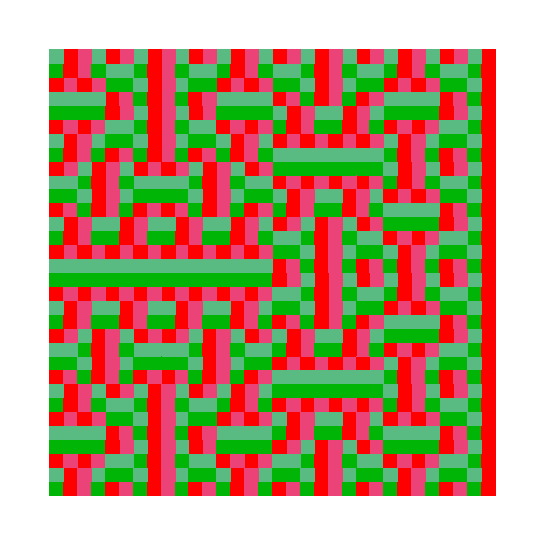

```mathematica
Graphics[polygonsColors[ComputeLocations[N[supertile[1,2]]],Map[#⟦1⟧&,supertile[1,2]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,3]]],Map[#⟦1⟧&,supertile[1,3]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,4]]],Map[#⟦1⟧&,supertile[1,4]]]]
Graphics[polygonsColorsPlain[ComputeLocations[N[supertile[1,5]]],Map[#⟦1⟧&,supertile[1,5]]]]
```

## 3.Computing Collared Tiles, stableEdges, collaredVertices (run 1,2)

```mathematica
timingList1={};
tiles=Expand[FullSimplify[supertile[1,5]]];
(*tilesLocations={tile1_written_as_list_of_locations, length of tile2_written_as_list_of_locations,...}. *)
AppendTo[timingList1,Timing[tilesLocations=ComputeLocations[tiles];"tilesLocations"]];
tilesLengths=Map[Length,tilesLocations];
(*tilesLocationsAsEdges={tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_of_positive_edges,...}. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
(*tilesEdgesDirections= directions of each tile where 1= same direction, -1=opposite directions. tile has counterclockwise direction. edge has positive direction.*)
(*AppendTo[timingList1,Timing[tilesEdgesDirections=Map[computeEdgesDirections,tilesLocations];"tilesEdgesDirections"]];*)
AppendTo[timingList1,Timing[tilesEdgesDirections=Map[prototilesDirections⟦#⟦1⟧⟧&,tiles];"tilesEdgesDirections"]];

computePositiveEdgesLocations=Function[{index},Module[{edge,lastedge,tileLocations},
tileLocations=tilesLocations⟦index⟧;
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[tilesEdgesDirections⟦index⟧⟦i⟧==1,edge,{edge⟦2⟧,edge⟦1⟧}],{i,1,Length[tileLocations]-1}],If[tilesEdgesDirections⟦index⟧⟦Length[tileLocations]⟧==1,{lastedge},{{lastedge⟦2⟧,lastedge⟦1⟧}}]]]];
AppendTo[timingList1,Timing[tilesLocationsAsEdges=Table[computePositiveEdgesLocations[i],{i,1,Length[tilesLocations]}];"tilesLocationsAsEdges"]];
(*accumulationsOfTilesLengths=Accumulate[{length of tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_positive_edges,... }]*)
accumulationsOfTilesLengths=Accumulate[tilesLengths];
(*tilesLocationsAsEdgesFlattened = list of all edges as pairs of locations (in the supertile)*)
tilesLocationsAsEdgesFlattened=Flatten[tilesLocationsAsEdges,1];
(*commonTilesLocationsAsEdgesIndices gives keysE and edgesToEdgesOfTiles (read below)*)
AppendTo[timingList1,Timing[positionIndexOftilesLocationsAsEdgesFlattened=Normal[PositionIndex[tilesLocationsAsEdgesFlattened]];"positionIndexOftilesLocationsAsEdgesFlattened"]];
(*edgesLocations = unique positive edges (i.e. the location of the positive edge is unique) *)
edgesLocations=Keys[positionIndexOftilesLocationsAsEdgesFlattened];
(*edgesToEdgesOfTiles = {{i1,i2},{i3,i4}...} where the positive edges at i1,i2, in tilesLocationsAsEdgesFlattened are the same.  *)
edgesToEdgesOfTiles=Values[positionIndexOftilesLocationsAsEdgesFlattened];
(*if {i1,i2} has length 2 then the edge at i1,i2 is an interior edge of the supertile. If it has length 1 then it is a bounded edge of the supertile:*)
{bEdges,iEdges}=Values[Sort[Normal[PositionIndex[Map[Length,edgesToEdgesOfTiles]]]]];
(*{bEdges,iEdges}=Values[PositionIndex[Map[Length,edgesToEdgesOfTiles]]];*)
iEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[iEdges]];
bEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[bEdges]];
iEdgesToSingletEdges=Map[#⟦1⟧&,iEdgesToEdgesOfTiles];
iEdgesLocations=tilesLocationsAsEdgesFlattened[[iEdgesToSingletEdges]];
bEdgesLocations=tilesLocationsAsEdgesFlattened[[Flatten[bEdgesToEdgesOfTiles]]];
(*  The tiling T contains the supertile; thus interior edges of the supertile are edges of the tiling T.
 An edge of the tiling T is a pair {(tile,indexOfEdgeInPrototile),(tile,indexOfEdgeInPrototile)}.
 edgeAsPairsOfPrototileNumbers =  {{prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}} Dictionary-sorted.
iEdgesAsPairsOfPrototileNumbers =  { Sort({prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}),...} !!This list has lots of multiplicities! *)
(*an interior edge in the supertile is a pair of edges that have common locations*)
bsearchMaxInaccumulationsOfTilesLengths[elem_]:=Module[{n0=1,n1=Length[accumulationsOfTilesLengths],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[accumulationsOfTilesLengths[[m]]==elem,While[accumulationsOfTilesLengths[[m]]==elem,m--];
Return[m+1]];
If[accumulationsOfTilesLengths[[m]]<elem,n0=m+1,n1=m-1]];
If[accumulationsOfTilesLengths[[m]]>elem,m,m+1]];

Clear[t1,i1,t2,i2]
unflattentedgeflattened=Function[tedgeflattenedNumber,Module[{tileNumber},
tileNumber=bsearchMaxInaccumulationsOfTilesLengths[tedgeflattenedNumber];
{tileNumber,If[tileNumber==1, tedgeflattenedNumber, tedgeflattenedNumber-accumulationsOfTilesLengths⟦tileNumber-1⟧]}]];
iEdgesAsPairsOfTiles=Map[Apply[Sort[{unflattentedgeflattened[#1],unflattentedgeflattened[#2]}]&,#]&,iEdgesToEdgesOfTiles];
iEdgesAsPairsOfPrototileNumbers=Table[{{t1,i1},{t2,i2}}=iEdgesAsPairsOfTiles⟦i⟧;Sort[{{tiles⟦t1⟧⟦1⟧,i1},{tiles⟦t2⟧⟦1⟧,i2}}],{i,1,Length[iEdgesAsPairsOfTiles]}];
Clear[t1,i1,t2,i2]
```

```mathematica
Take[tiles,10]//ColumnForm
tilesLocationsAsEdges//Length
```

{3,{0,0}}
{1,{1,0}}
{1,{1,1}}
{4,{0,1}}
{2,{2,0}}
{3,{3,0}}
{4,{3,1}}
{2,{2,1}}
{1,{2,2}}
{2,{3,2}}

1024

```mathematica
timingList1//ColumnForm
```

{0.01111,tilesLocations}
{0.00114,tilesEdgesDirections}
{0.02768,tilesLocationsAsEdges}
{0.00533,positionIndexOftilesLocationsAsEdgesFlattened}

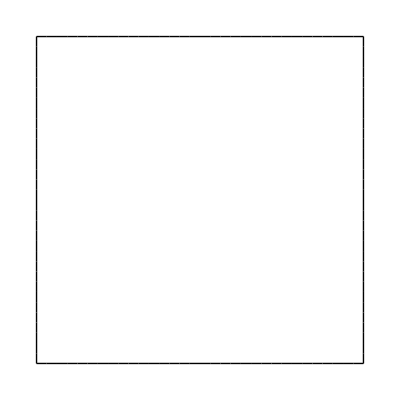

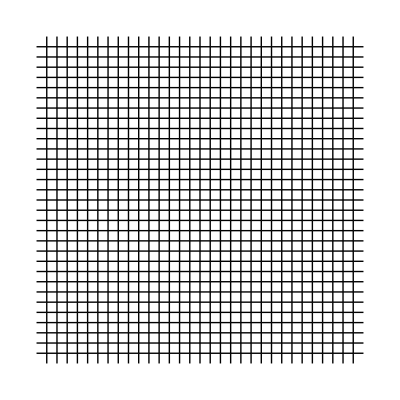

```mathematica
Graphics[Line[bEdgesLocations]]
Graphics[Line[iEdgesLocations]]
```

```mathematica
(*iEdgesAsPairsOfPrototileNumbers[[3]]
tilesLocationsAsEdges[[1]]
tilesLocationsAsEdges[[1]][[3]]
tilesLocationsAsEdges[[3]]
tilesLocationsAsEdges[[3]][[6]]*)
```

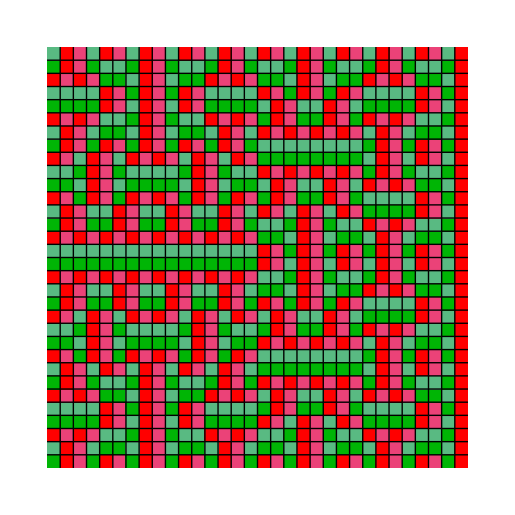

```mathematica
Show[Graphics[polygonsColorsPlain[ComputeLocations[supertile[1,5]],Map[#⟦1⟧&,supertile[1,5]]]],Graphics[Line[iEdgesLocations]]]
```

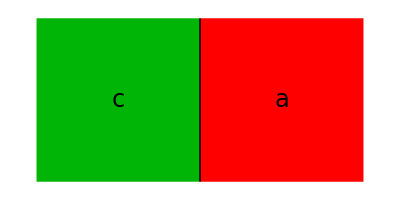

```mathematica
(*drawiEdges=Function[ieNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];*)
drawiEdges=Function[ieNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];
drawiEdges[1]
```

```mathematica
iEdgesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[iEdgesAsPairsOfPrototileNumbers]]];
(*for block tilings only ie. rectangular tilings:*)
verticalEdgeQ=Function[{v1,v2},If[v1⟦1⟧==v2⟦1⟧,True,False]];
horizontalEdgeQ=Function[{v1,v2},If[v1⟦2⟧==v2⟦2⟧,True,False]];
drawiEdgesLatex=Function[ieNum,Module[{Label12Line12,L1,L2,p1,p2,isHorizontalEdge,isVerticalEdge,lbl,lin},
Label12Line12={polygonsLabels[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]};
{{{L1,p1},{L2,p2}},lin}=Label12Line12;
isHorizontalEdge=horizontalEdgeQ[lin⟦1⟧⟦1⟧,lin⟦1⟧⟦2⟧];
isVerticalEdge=verticalEdgeQ[lin⟦1⟧⟦1⟧,lin⟦1⟧⟦2⟧];
(*read from left to right and from bottom to top*)
If[isVerticalEdge,If[p1⟦1⟧<p2⟦1⟧,lbl={L1,L2},lbl={L2,L1}]];
If[isHorizontalEdge,If[p1⟦2⟧<p2⟦2⟧,lbl={L1,L2},lbl={L2,L1}]];
{isHorizontalEdge,lbl,ieNum}
]];
iEdgesRepresentatives=Transpose[Sort[Map[drawiEdgesLatex,iEdgesRepresentatives]]]⟦3⟧
(*output: {isHorizontalEdge,labelsReadFromLeftToRightOrFromBottomToTop,representativenumber}*)
stableEdgesLatex=Map[drawiEdgesLatex,iEdgesRepresentatives]
{list1,list2,list3}=Transpose[stableEdgesLatex];
(*output: horizontal edges ,vertical edges:*)
sEdgesVertical=DeleteCases[Table[If[list1[[i]]==False,list2[[i]]],{i,1,Length[list1]}],Null];
sEdgesHorizontal=DeleteCases[Table[If[list1[[i]]==True,list2[[i]]],{i,1,Length[list1]}],Null];
Table[
StringForm["\\vsE{``}{``},\\,",sEdgesVertical⟦i⟧⟦1⟧,sEdgesVertical⟦i⟧⟦2⟧],{i,1,Length[sEdgesVertical]}]//ColumnForm
Table[
StringForm["\\hsE{``}{``},\\,",sEdgesHorizontal⟦i⟧⟦1⟧,sEdgesHorizontal⟦i⟧⟦2⟧],{i,1,Length[sEdgesHorizontal]}]//ColumnForm
```

{3,19,9,15,1,24,37,7,13,59,4,6,18,16,10,21,2,8,14,48}

{{False,{a,b},3},{False,{b,a},19},{False,{b,c},9},{False,{b,d},15},{False,{c,a},1},{False,{c,c},24},{False,{c,d},37},{False,{d,a},7},{False,{d,c},13},{False,{d,d},59},{True,{a,a},4},{True,{a,b},6},{True,{a,c},18},{True,{b,a},16},{True,{b,b},10},{True,{b,c},21},{True,{c,d},2},{True,{d,a},8},{True,{d,b},14},{True,{d,c},48}}

\vsE{a}{b},\,
\vsE{b}{a},\,
\vsE{b}{c},\,
\vsE{b}{d},\,
\vsE{c}{a},\,
\vsE{c}{c},\,
\vsE{c}{d},\,
\vsE{d}{a},\,
\vsE{d}{c},\,
\vsE{d}{d},\,

\hsE{a}{a},\,
\hsE{a}{b},\,
\hsE{a}{c},\,
\hsE{b}{a},\,
\hsE{b}{b},\,
\hsE{b}{c},\,
\hsE{c}{d},\,
\hsE{d}{a},\,
\hsE{d}{b},\,
\hsE{d}{c},\,

```mathematica
iEdgesRepresentatives//Length
sEdges=iEdgesAsPairsOfPrototileNumbers⟦iEdgesRepresentatives⟧
drawsEdges=Function[i,drawiEdges[iEdgesRepresentatives⟦i⟧]];
drawWsEdges=Function[seNum,Module[{se,wse},
se=Map[#⟦1⟧&,iEdgesAsPairsOfTiles⟦iEdgesRepresentatives⟦seNum⟧⟧];
wse=Flatten[Map[ωTile[tiles⟦#⟧]&,se],1];
Graphics[Join[polygonsColors[ComputeLocations[wse],Map[#⟦1⟧&,wse]],Map[Line,λ ComputeLocations[tiles⟦se⟧]]]]]];
```

20

{{{1,2},{2,4}},{{1,4},{2,2}},{{2,2},{3,4}},{{2,2},{4,4}},{{1,4},{3,2}},{{3,2},{3,4}},{{3,2},{4,4}},{{1,4},{4,2}},{{3,4},{4,2}},{{4,2},{4,4}},{{1,1},{1,3}},{{1,3},{2,1}},{{1,3},{3,1}},{{1,1},{2,3}},{{2,1},{2,3}},{{2,3},{3,1}},{{3,3},{4,1}},{{1,1},{4,3}},{{2,1},{4,3}},{{3,1},{4,3}}}

20

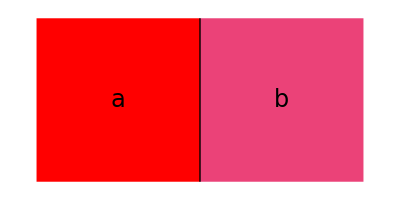
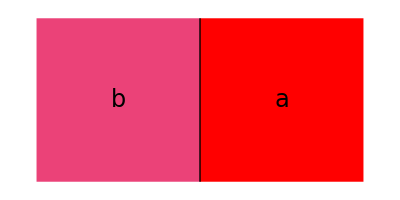
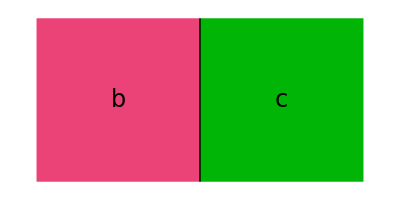
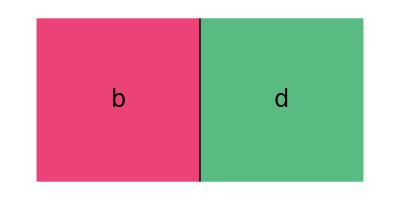
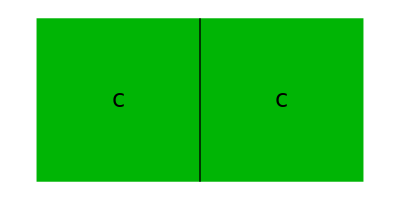
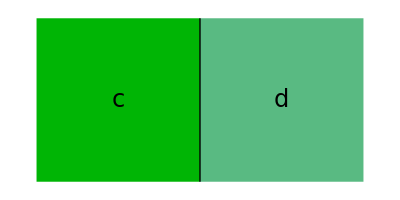
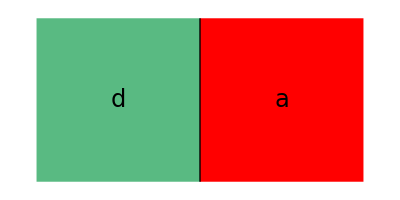
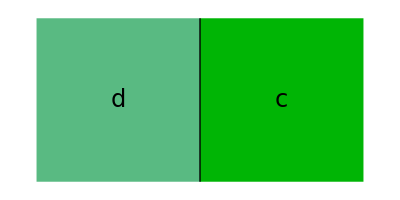
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*sEdges*)
iEdgesRepresentatives//Length
Map[drawiEdges,iEdgesRepresentatives]
```

```mathematica
prototiles//Length
```

4

```mathematica
(*iedgesLocationsAsVertices={positive_edge1, positive_edge2,...}, where these edges are interior edges of the supertile written as positive edges and their location is unique. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
iedgesLocationsAsVertices=iEdgesLocations;
(*iedgesLocationsAsVerticesFlattened = all possible vertices as locations (coming from the interior edges in the supertile)*)
iedgesLocationsAsVerticesFlattened=Flatten[iedgesLocationsAsVertices,1];
(*commonVerticesIndicesInEdgesLocationsAsVertices gives keysV and valuesV (read below)*)
positionIndexOfiedgesLocationsAsVerticesFlattened=PositionIndex[iedgesLocationsAsVerticesFlattened];
(*keysV = unique vertices (their location is unique) *)
verticesLocations=Keys[positionIndexOfiedgesLocationsAsVerticesFlattened];(*representatives of common locations of the vertices*)
(*valuesV = {{i1,i2...},{j3,j4...}...} where the vertices at i1,i2, in iedgesLocationsAsVerticesFlattened are the same. The goal is to obtain the edges with common vertices  *)
verticesToVerticesOfiEdges=Values[positionIndexOfiedgesLocationsAsVerticesFlattened];(* indices of keysV*)
(*if {i1,i2..} has length >1 then the vertex at i1,i2... is an interior vertex of the interior_edges of the supertile. 
If it has length 1 then it is a boundary vertex of the interior_edges of the supertile:*)

{boundaryVertices,interiorVertices}=Values[Sort[Normal[PositionIndex[Map[Length[#]>MAXDegreeOfBoundaryVertices&,verticesToVerticesOfiEdges]]]]];
interiorVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[interiorVertices]];
boundaryVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[boundaryVertices]];
interiorVerticesToSingleVerticesOfiEdges=Map[#⟦1⟧&,interiorVerticesToVerticesOfiEdges];
interiorVerticesLocations=iedgesLocationsAsVerticesFlattened[[interiorVerticesToSingleVerticesOfiEdges]];
boundaryVerticesLocations=iedgesLocationsAsVerticesFlattened[[Flatten[boundaryVerticesToVerticesOfiEdges]]];
tileNumberEdgeVertexTotileNumberVertex=Function[tileNumberEdgeVertex,Module[{tileNumber,edgeNumberOnTile,vertexNumberOnEdge,initialOrFinalVertexOnEdge,edgeDirection,vertexNumberOnTile},
{{tileNumber,edgeNumberOnTile},vertexNumberOnEdge}=tileNumberEdgeVertex;
edgeDirection=tilesEdgesDirections[[tileNumber]][[edgeNumberOnTile]];
vertexNumberOnTile=edgeNumberOnTile;
If[(edgeDirection==1 && vertexNumberOnEdge==2)||(edgeDirection==-1 && vertexNumberOnEdge==1),vertexNumberOnTile=Mod[vertexNumberOnTile+1,tilesLengths[[tileNumber]],1]];
{tileNumber,vertexNumberOnTile}]];

unflatteniEvertexflattened=Function[ievertexflattenedNumber,
{IntegerPart[(ievertexflattenedNumber+1)/2],Mod[ievertexflattenedNumber,2,1]}];
(*verticesAsListOfIndicesOfTiles={ (iEdgesAsPairsOfPrototileNumbers[positive_edge_i_index], 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
interiorVerticesAsiEdges=Table[Sort[Table[unflatteniEvertexflattened[interiorVerticesToVerticesOfiEdges⟦j⟧⟦i⟧],{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

(*protoVerticesAsListOfIndicesOfEdges={ (positive_edge_i_index, 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
verticesAsListOfTilesEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfTiles⟦iEdgeNumber⟧,index},{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

verticesAsListOfTilesVNumbers=Table[Union[Flatten[Table[{{e1,e2},v}=verticesAsListOfTilesEVNumbers[[j]][[i]];
{tileNumberEdgeVertexTotileNumberVertex[{e1,v}],
tileNumberEdgeVertexTotileNumberVertex[{e2,v}]},{i,1,Length[verticesAsListOfTilesEVNumbers[[j]]]}],1]],{j,1,Length[verticesAsListOfTilesEVNumbers]}];

verticesAsListOfPrototileEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfPrototileNumbers⟦iEdgeNumber⟧,index},
{i,1,Length[interiorVerticesAsiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesAsiEdges]}];

verticesAsListOfPrototileVNumbers=Table[Sort[Table[
{tileNumber,index}=verticesAsListOfTilesVNumbers⟦j⟧⟦i⟧;
{tiles⟦tileNumber⟧⟦1⟧,index},
{i,1,Length[verticesAsListOfTilesVNumbers⟦j⟧]}]],{j,1,Length[verticesAsListOfTilesVNumbers]}];
```

```mathematica
verticesAsListOfPrototileVNumbers//Tally//Length
Take[verticesAsListOfPrototileVNumbers//Tally,10]//ColumnForm
```

24

{{{1,1},{1,4},{3,3},{4,2}},79}
{{{1,2},{1,3},{2,1},{2,4}},87}
{{{1,1},{1,3},{2,2},{2,4}},17}
{{{1,2},{1,4},{2,1},{4,3}},29}
{{{2,2},{2,3},{3,4},{4,1}},58}
{{{1,4},{3,1},{3,3},{4,2}},29}
{{{2,2},{3,4},{4,1},{4,3}},39}
{{{1,2},{2,1},{2,3},{4,4}},29}
{{{1,3},{2,4},{3,1},{3,2}},68}
{{{1,4},{2,3},{3,1},{3,2}},29}

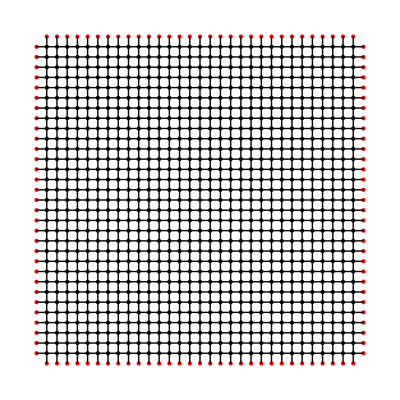

```mathematica
(*boundary vertices should be shown in RED. Interior vertices in Black *)
Show[Graphics[{Red,Point[boundaryVerticesLocations]}],
Graphics[Point[interiorVerticesLocations]],Graphics[Line[iEdgesLocations]]]
```

```mathematica
iEdgesToEdgesOfTiles[[{1,2,5}]]==edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,iEdgesToEdgesOfTiles[[{1,2,5}]]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]]]]
```

True

True

True

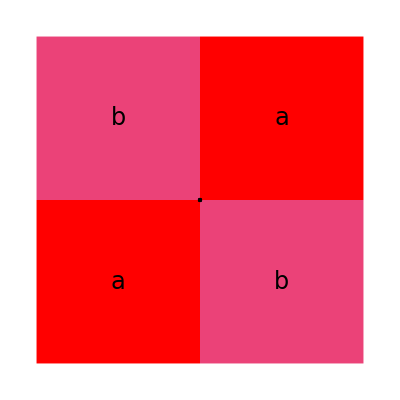

```mathematica
(*drawInteriorVertex=Function[ivNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];*)
drawInteriorVertex=Function[ivNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];
drawInteriorVertex[3]
```

```mathematica
iVerticesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[verticesAsListOfPrototileVNumbers]]];
(*only for block tilings i.e. rectangular tilings:*)
drawInteriorVertexLatex=Function[ivNum,Module[{L1,L2,L3,L4,p1,p2,p3,p4,point,pt,loc},
{{{L1,p1},{L2,p2},{L3,p3},{L4,p4}},point}={polygonsLabels[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]};
loc={0,0,0,0};
pt=point⟦1⟧⟦1⟧;
If[(p1-pt)⟦1⟧>0 ,
If[(p1-pt)⟦2⟧>0,loc⟦3⟧={L1,p1},loc⟦2⟧={L1,p1}],
If[(p1-pt)⟦2⟧>0,loc⟦4⟧={L1,p1},loc⟦1⟧={L1,p1}]];
If[(p2-pt)⟦1⟧>0 ,
If[(p2-pt)⟦2⟧>0,loc⟦3⟧={L2,p2},loc⟦2⟧={L2,p2}],
If[(p2-pt)⟦2⟧>0,loc⟦4⟧={L2,p2},loc⟦1⟧={L2,p2}]];
If[(p3-pt)⟦1⟧>0 ,
If[(p3-pt)⟦2⟧>0,loc⟦3⟧={L3,p3},loc⟦2⟧={L3,p3}],
If[(p3-pt)⟦2⟧>0,loc⟦4⟧={L3,p3},loc⟦1⟧={L3,p3}]];
If[(p4-pt)⟦1⟧>0 ,
If[(p4-pt)⟦2⟧>0,loc⟦3⟧={L4,p4},loc⟦2⟧={L4,p4}],
If[(p4-pt)⟦2⟧>0,loc⟦4⟧={L4,p4},loc⟦1⟧={L4,p4}]];
Flatten[{Transpose[loc],ivNum},1]
]
];
iVerticesRepresentatives=Transpose[Sort[Map[drawInteriorVertexLatex,iVerticesRepresentatives]]][[3]]
(*output: (bottomleft, bottomright,topright,topleft) i.e. counterclowise starting from the bottomleft:*)
stableVerticesLatex=Transpose[Map[drawInteriorVertexLatex,iVerticesRepresentatives]]⟦1⟧
Table[
StringForm["\\sVf{``}{``}{``}{``},\\,",stableVerticesLatex⟦i⟧⟦1⟧,stableVerticesLatex⟦i⟧⟦2⟧,stableVerticesLatex⟦i⟧⟦3⟧,stableVerticesLatex⟦i⟧⟦4⟧],{i,1,Length[stableVerticesLatex]}]//ColumnForm
```

{3,56,2,51,9,55,10,5,18,11,8,30,1,6,13,50,19,24,4,34,7,67,54,31}

{{a,b,a,b},{a,b,a,c},{a,b,b,a},{a,b,c,b},{a,b,c,c},{b,a,b,a},{b,a,c,c},{b,c,d,b},{b,c,d,c},{b,d,a,c},{b,d,b,a},{b,d,c,b},{c,a,a,d},{c,a,c,d},{c,c,d,d},{c,d,a,d},{c,d,c,d},{d,a,a,c},{d,a,b,a},{d,a,c,b},{d,c,d,b},{d,c,d,c},{d,d,a,b},{d,d,b,a}}

\sVf{a}{b}{a}{b},\,
\sVf{a}{b}{a}{c},\,
\sVf{a}{b}{b}{a},\,
\sVf{a}{b}{c}{b},\,
\sVf{a}{b}{c}{c},\,
\sVf{b}{a}{b}{a},\,
\sVf{b}{a}{c}{c},\,
\sVf{b}{c}{d}{b},\,
\sVf{b}{c}{d}{c},\,
\sVf{b}{d}{a}{c},\,
\sVf{b}{d}{b}{a},\,
\sVf{b}{d}{c}{b},\,
\sVf{c}{a}{a}{d},\,
\sVf{c}{a}{c}{d},\,
\sVf{c}{c}{d}{d},\,
\sVf{c}{d}{a}{d},\,
\sVf{c}{d}{c}{d},\,
\sVf{d}{a}{a}{c},\,
\sVf{d}{a}{b}{a},\,
\sVf{d}{a}{c}{b},\,
\sVf{d}{c}{d}{b},\,
\sVf{d}{c}{d}{c},\,
\sVf{d}{d}{a}{b},\,
\sVf{d}{d}{b}{a},\,

```mathematica
iVerticesRepresentatives//Length
cVertices=verticesAsListOfPrototileVNumbers⟦iVerticesRepresentatives⟧
drawcVertices=Function[index,drawInteriorVertex[iVerticesRepresentatives⟦index⟧]];
drawWcVertices=Function[cvNum,Module[{cv,wcv},
cv=Map[#⟦1⟧&,verticesAsListOfTilesVNumbers⟦iVerticesRepresentatives⟦cvNum⟧⟧];
wcv=Flatten[Map[ωTile[tiles⟦#⟧]&,cv],1];
Graphics[Join[polygonsColors[ComputeLocations[wcv],Map[#⟦1⟧&,wcv]],Map[Line,λ ComputeLocations[tiles⟦cv⟧]]]]]];
```

24

{{{1,1},{1,3},{2,2},{2,4}},{{1,1},{1,3},{2,4},{3,2}},{{1,2},{1,3},{2,1},{2,4}},{{1,3},{2,2},{2,4},{3,1}},{{1,3},{2,4},{3,1},{3,2}},{{1,2},{1,4},{2,1},{2,3}},{{1,4},{2,3},{3,1},{3,2}},{{2,2},{2,3},{3,4},{4,1}},{{2,3},{3,2},{3,4},{4,1}},{{1,1},{2,3},{3,2},{4,4}},{{1,2},{2,1},{2,3},{4,4}},{{2,2},{2,3},{3,1},{4,4}},{{1,1},{1,4},{3,3},{4,2}},{{1,4},{3,1},{3,3},{4,2}},{{3,3},{3,4},{4,1},{4,2}},{{1,1},{3,3},{4,2},{4,4}},{{3,1},{3,3},{4,2},{4,4}},{{1,1},{1,4},{3,2},{4,3}},{{1,2},{1,4},{2,1},{4,3}},{{1,4},{2,2},{3,1},{4,3}},{{2,2},{3,4},{4,1},{4,3}},{{3,2},{3,4},{4,1},{4,3}},{{1,1},{2,2},{4,3},{4,4}},{{1,2},{2,1},{4,3},{4,4}}}

24

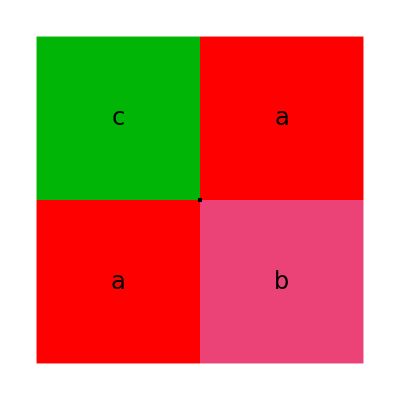
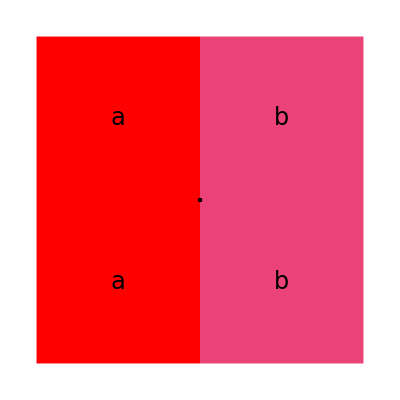
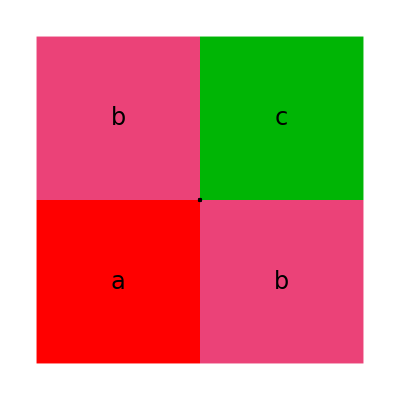
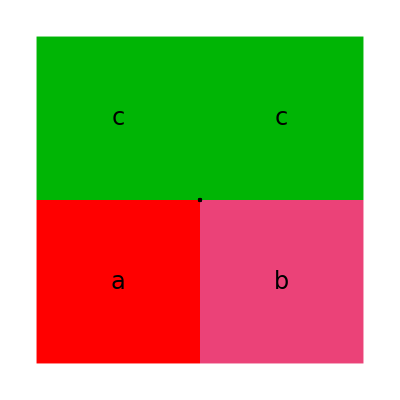
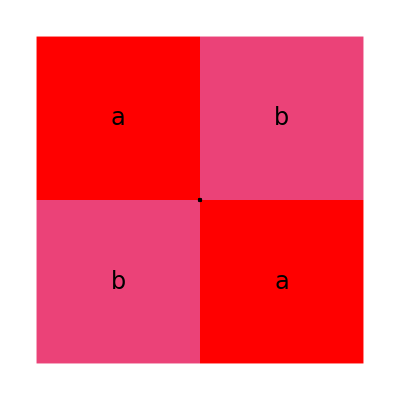
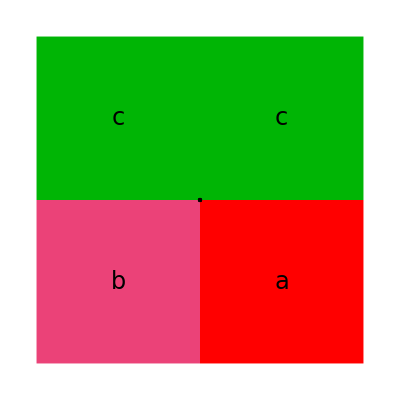
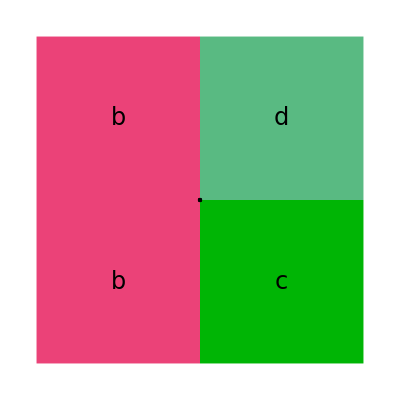
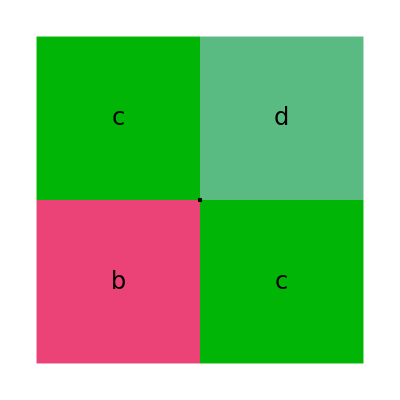
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* protovertices == collared vertices *)
iVerticesRepresentatives//Length
Map[drawInteriorVertex,iVerticesRepresentatives]
```

### results

```mathematica
sEdges
```

{{{1,2},{2,4}},{{1,4},{2,2}},{{2,2},{3,4}},{{2,2},{4,4}},{{1,4},{3,2}},{{3,2},{3,4}},{{3,2},{4,4}},{{1,4},{4,2}},{{3,4},{4,2}},{{4,2},{4,4}},{{1,1},{1,3}},{{1,3},{2,1}},{{1,3},{3,1}},{{1,1},{2,3}},{{2,1},{2,3}},{{2,3},{3,1}},{{3,3},{4,1}},{{1,1},{4,3}},{{2,1},{4,3}},{{3,1},{4,3}}}

```mathematica
cVertices
```

{{{1,1},{1,3},{2,2},{2,4}},{{1,1},{1,3},{2,4},{3,2}},{{1,2},{1,3},{2,1},{2,4}},{{1,3},{2,2},{2,4},{3,1}},{{1,3},{2,4},{3,1},{3,2}},{{1,2},{1,4},{2,1},{2,3}},{{1,4},{2,3},{3,1},{3,2}},{{2,2},{2,3},{3,4},{4,1}},{{2,3},{3,2},{3,4},{4,1}},{{1,1},{2,3},{3,2},{4,4}},{{1,2},{2,1},{2,3},{4,4}},{{2,2},{2,3},{3,1},{4,4}},{{1,1},{1,4},{3,3},{4,2}},{{1,4},{3,1},{3,3},{4,2}},{{3,3},{3,4},{4,1},{4,2}},{{1,1},{3,3},{4,2},{4,4}},{{3,1},{3,3},{4,2},{4,4}},{{1,1},{1,4},{3,2},{4,3}},{{1,2},{1,4},{2,1},{4,3}},{{1,4},{2,2},{3,1},{4,3}},{{2,2},{3,4},{4,1},{4,3}},{{3,2},{3,4},{4,1},{4,3}},{{1,1},{2,2},{4,3},{4,4}},{{1,2},{2,1},{4,3},{4,4}}}

```mathematica
sEdges//Length
cVertices//Length
```

20

24

## 4. Exponential Matrix, Index Matrix (run 1,2,3)

```mathematica
(*exponential matrix*)
cVerticesAssEdges=verticesAsListOfPrototileEVNumbers[[iVerticesRepresentatives]];
sEdgescVerticesMatrix=ConstantArray[0,{Length[sEdges],Length[cVertices]}];

sEdgescVerticesMatrixIndicesFunction=
Function[cvNumber,Module[{cv,se,vInitialOrFinal,seNumber,value},
cv=cVerticesAssEdges⟦cvNumber⟧;
Table[{se,vInitialOrFinal}=cv⟦i⟧;
seNumber=Position[sEdges,se]⟦1⟧⟦1⟧;
value=If[vInitialOrFinal==1,-1,1];
sEdgescVerticesMatrix⟦seNumber⟧⟦cvNumber⟧+=value;
{{seNumber,cvNumber},value},{i,1,Length[cv]}]]];


sEdgescVerticesMatrixIndices=Table[sEdgescVerticesMatrixIndicesFunction[i],{i,1,Length[cVertices]}];
(*stableEdges-collardVertices Matrix (se1=-cv1+cv9+cv14...*)
Print["δ^0=",sEdgescVerticesMatrix//MatrixForm]
```

δ^0=(1 | 1 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
(*Index Matrix*)
prototilessEdgesMatrix=ConstantArray[0,{Length[prototiles],Length[sEdges]}];
Table[{{p1,e1},{p2,e2}}=sEdges⟦sedgeNumber⟧;
prototilessEdgesMatrix⟦p1⟧⟦sedgeNumber⟧+=prototilesDirections⟦p1⟧⟦e1⟧;
prototilessEdgesMatrix⟦p2⟧⟦sedgeNumber⟧+=prototilesDirections⟦p2⟧⟦e2⟧;,
{sedgeNumber,1,Length[sEdges]}];
Print["δ^1=",prototilessEdgesMatrix//MatrixForm]
```

δ^1=(1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0
0 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 1
0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1)

```mathematica
prototilessEdgesMatrix.sEdgescVerticesMatrix//Max
prototilessEdgesMatrix.sEdgescVerticesMatrix//Min
```

0

0

## 5. Homotopy matrices Wv, We, Wf

```mathematica
(*Homotopy ω(prototile) --> prototile : Hverticesp1t1 is the image of the map on the vertices from ω(prototile) to same protitile 1.*)


Hverticesp1t1={1,2,3,4};
Hverticesp1t2={2,2,3,3};
Hverticesp1t3={3,3,3,3};
Hverticesp1t4={4,3,3,4};

Hverticesp1={Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4};

Hvertices={Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1}
```

{{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}}}

```mathematica
Hvertices
```

{{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}}}

```mathematica
Table[Map[Length,Hvertices⟦i⟧],{i,1,Length[Hvertices]}]==Map[prototilesLengths⟦#⟧&,wPrototileNumbers]
```

True

```mathematica
HverticesSimple=Hvertices
```

{{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}},{{1,2,3,4},{2,2,3,3},{3,3,3,3},{4,3,3,4}}}

```mathematica
drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{arrows}]];

drawHomotopycVertices=Function[cVertexNum,Module[{cv},
cv=cVertices⟦cVertexNum⟧;
Graphics[Map[drawHomotopyVerticesOfTilesNoGraphics,Table[{cv⟦i,1⟧,Expand[FullSimplify[prototiles⟦cv⟦i,1⟧,1⟧-prototiles⟦cv⟦i,1⟧,cv⟦i,2⟧⟧]]},{i,1,Length[cv]}]]]]];

drawHomotopyVerticesOfTiles=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]]];

drawHomotopyVertices=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

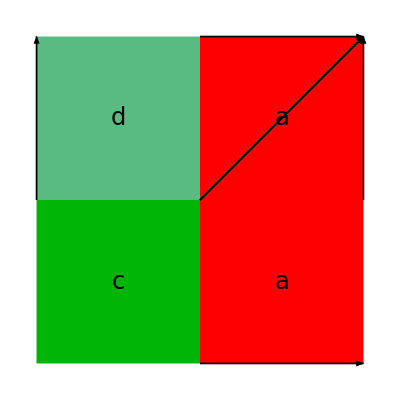
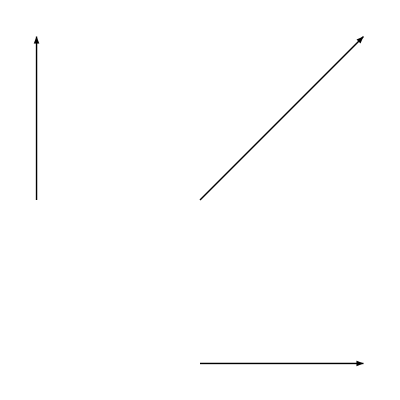
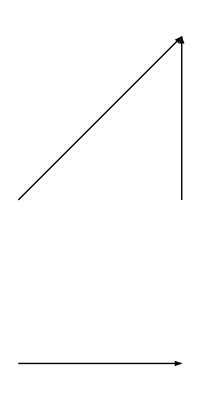
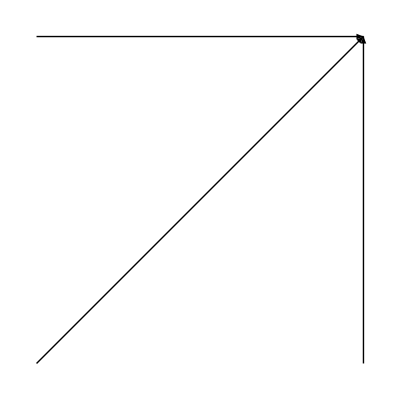
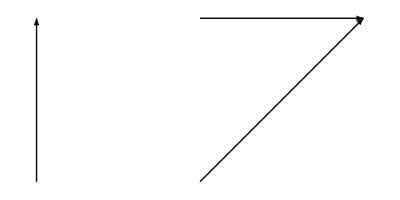
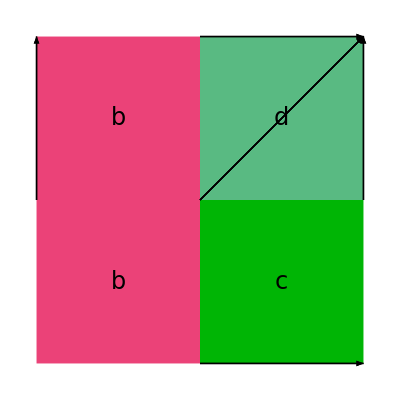
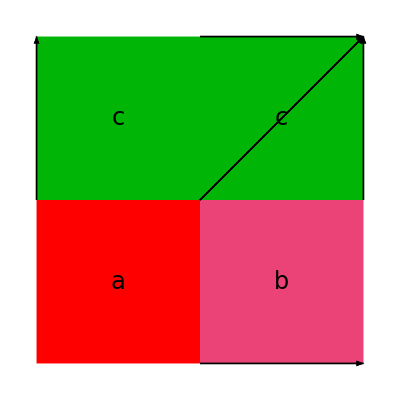
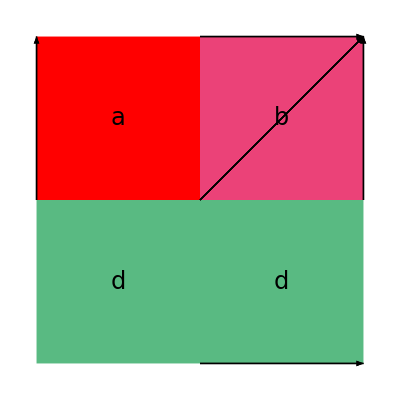
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[drawHomotopyVerticesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

```mathematica
Table[drawHomotopyVertices[i],{i,1,Length[prototiles]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

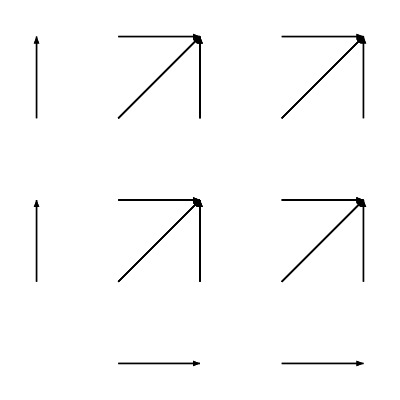
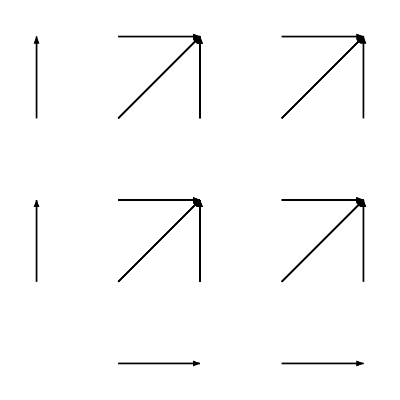
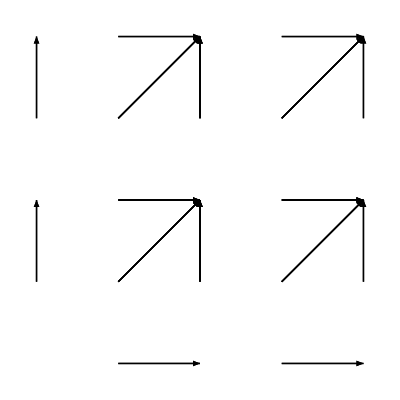
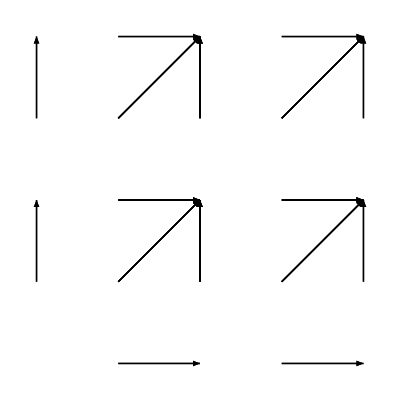
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[drawHomotopycVertices[i],{i,1,Length[cVertices]}]
```

```mathematica
homotopycVertices=ConstantArray[0,Length[cVertices]];

Clear[cv,ps,vs,locsH,xx,yy,ts,cvNum]
For[cvNum=1,cvNum≤ Length[cVertices],cvNum++,
cv=cVertices⟦cvNum⟧;
cvHpreimage=Table[Position[HverticesSimple⟦cv⟦i,1⟧⟧,cv⟦i,2⟧],{i,1,Length[cv]}];
{ps,vs}=Transpose[cv];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototiles⟦ps⟦i⟧⟧⟦vs⟦i⟧⟧},{i,1,Length[ps]}];
(*Map[ωTile,ts]*)
locsH=Table[Expand[FullSimplify[ComputeLocations[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
cvHpreimageLocations=Table[Table[locsH⟦j⟧⟦cvHpreimage⟦j⟧⟦i,1⟧,cvHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[cvHpreimage⟦j⟧]}],{j,1,Length[cvHpreimage]}];
(*cvHpreimage//ColumnForm*)
(*cvHpreimageLocations//Point//Graphics*)
(*Flatten[cvHpreimageLocations,1]*)
cvHpreimageFlattened=Flatten[cvHpreimage,1];
(*cvHpreimageFlattenedTiles=Flatten[Table[ConstantArray[i,Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1]*)
cvHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1];
hcverticesindices=Values[Normal[PositionIndex[Flatten[cvHpreimageLocations,1]]]];

(*hcverticesAsTiles=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedTiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[Flatten[{yy⟦i⟧,xx⟦i⟧}],{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}]
Table[Map[locsH⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧&,hcverticesAsTiles⟦i⟧],{i,1,Length[hcverticesAsTiles]}]*)

hcvertices=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedPrototiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}];
homotopycVertices⟦cvNum⟧=Table[Position[cVertices,hcvertices⟦i⟧]⟦1,1⟧,{i,1,Length[hcvertices]}]]
homotopycVertices
```

{{5,13,3,20},{4,13,3,19},{18,3,13,3},{13,3,2,20},{13,3,1,19},{10,24,15,8},{15,23,8,11},{12,22,8,14},{8,14,21,11},{20,8,16,11},{10,19,8,16},{12,18,8,16},{17,9,5,15},{9,16,5,15},{5,7,15,15},{14,5,10,15},{13,5,10,15},{12,21,3,24},{2,11,21,24},{21,10,4,24},{4,9,20,24},{3,8,20,24},{7,4,24,23},{2,6,24,23}}

```mathematica
cverticesHMtx=ConstantArray[0,{Length[cVertices],Length[cVertices]}];
Table[Table[cverticesHMtx⟦homotopycVertices⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopycVertices⟦i⟧]}],{i,1,Length[homotopycVertices]}];
Print["W_V=",cverticesHMtx//MatrixForm]
```

W_V=(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
drawHomotopycVertices[2]
Map[drawcVertices,Transpose[cVertices⟦2⟧]⟦1⟧]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[1]
```

-Graphics-

```mathematica
protoEdgesAsPairsVerticesFunction=Function[protoedgesIndices,Table[{protoedgesIndices⟦i⟧,protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧},{i,1,Length[protoedgesIndices]}]];
protoEdgesAsPosPairsVerticesFunction=Function[{protoedgesIndices,protoedgesOrientations},Table[If[protoedgesOrientations⟦i⟧==1,{protoedgesIndices⟦i⟧,protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧},{protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧,protoedgesIndices⟦i⟧}],{i,1,Length[protoedgesIndices]}]];


(*initialVertexOfsEdgeNumFunction=Function[sedgeNum,initialVertexOfsEdgeFunction[sEdges⟦sedgeNum⟧]];
finalVertexOfsEdgeNumFunction=Function[sedgeNum,finalVertexOfsEdgeFunction[sEdges⟦sedgeNum⟧]];

initialVertexOfsEdgeFunction=Function[sedge,Sort[{{sedge⟦1⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦1⟧⟦1⟧,sedge⟦1⟧⟦2⟧⟧⟦1⟧},{sedge⟦2⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦2⟧⟦1⟧,sedge⟦2⟧⟦2⟧⟧⟦1⟧}}]];
finalVertexOfsEdgeFunction=Function[sedge,Sort[{{sedge⟦1⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦1⟧⟦1⟧,sedge⟦1⟧⟦2⟧⟧⟦2⟧},{sedge⟦2⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦2⟧⟦1⟧,sedge⟦2⟧⟦2⟧⟧⟦2⟧}}]];
rowForm=Function[lst,{lst}//MatrixForm];
*)

protoVertices=Map[Range,prototilesLengths];

protoEdgesAsPairsOfVertices=Table[protoEdgesAsPairsVerticesFunction[protoVertices⟦i⟧],{i,1,Length[prototiles]}]
protoEdgesAsPosPairsOfVertices=Table[protoEdgesAsPosPairsVerticesFunction[protoVertices⟦i⟧,prototilesDirections⟦i⟧],{i,1,Length[prototiles]}]
wPrototileAsprotoEdgesAsPosPairsOfVertices=Map[protoEdgesAsPosPairsOfVertices⟦#⟧&,wPrototileNumbers];
```

{{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}}}

{{{1,2},{2,3},{4,3},{1,4}},{{1,2},{2,3},{4,3},{1,4}},{{1,2},{2,3},{4,3},{1,4}},{{1,2},{2,3},{4,3},{1,4}}}

```mathematica
HedgesSameDirFunction=Function[{HverticesOfTile,tNumImage},
Table[If[Mod[HverticesOfTile⟦i⟧+1,prototilesLengths⟦tNumImage⟧,1]==HverticesOfTile⟦Mod[i+1,Length[HverticesOfTile],1]⟧,HverticesOfTile⟦i⟧,0],{i,1,Length[HverticesOfTile]}]];
HedgesOppositeDirFunction=Function[{HverticesOfTile,tNumImage},
Table[If[Mod[HverticesOfTile⟦i⟧-1,prototilesLengths⟦tNumImage⟧,1]==HverticesOfTile⟦Mod[i+1,Length[HverticesOfTile],1]⟧,Mod[HverticesOfTile⟦i⟧-1,prototilesLengths⟦tNumImage⟧,1],0],{i,1,Length[HverticesOfTile]}]];
joinSameOppDirHedgesFunction=Function[{sameDirHedges,oppDirHedges},
Table[Table[If[sameDirHedges⟦i⟧⟦j⟧≠0 &&oppDirHedges⟦i⟧⟦j⟧≠0,Print["Error:HedgeHasMultipleValues at {i,j}",{i,j}]];
If[sameDirHedges⟦i⟧⟦j⟧≠0,sameDirHedges⟦i⟧⟦j⟧,oppDirHedges⟦i⟧⟦j⟧],{j,1,Length[sameDirHedges⟦i⟧]}],{i,1,Length[sameDirHedges]}]];
```

```mathematica
HedgesTemp=Table[
sameDirHedges=Map[HedgesSameDirFunction[#,tNum]&,HverticesSimple⟦tNum⟧];
oppDirHedges=Map[HedgesOppositeDirFunction[#,tNum]&,HverticesSimple⟦tNum⟧];
joinSameOppDirHedgesFunction[sameDirHedges,oppDirHedges],{tNum,1,Length[prototiles]}];
Hedges=Table[{1,HedgesTemp⟦i⟧},{i,1,Length[HedgesTemp]}]
```

{{1,{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}}},{1,{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}}},{1,{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}}},{1,{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}}}}

```mathematica
HedgesSimple=Map[#⟦2⟧&,Hedges]
```

{{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}},{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}},{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}},{{1,2,3,4},{0,2,0,2},{0,0,0,0},{3,0,3,0}}}

```mathematica
prototilesMidEdges=Table[Table[Expand[FullSimplify[(prototiles⟦i⟧⟦j⟧+prototiles⟦i⟧⟦Mod[j+1,Length[prototiles⟦i⟧],1]⟧)/2]],{j,1,Length[prototiles⟦i⟧]}],{i,1,Length[prototiles]}];
ComputeLocationsMidEdges=Function[{tiles},Module[{prototileNumber,translation},Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototilesMidEdges⟦prototileNumber⟧⟦j⟧+translation,{j,1,Length[prototilesMidEdges⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];


drawHomotopyEdgesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[ωTile[tile]];
imageEdges=HedgesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{tile}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopysEdges=Function[sEdgeNum,Module[{se},
se=sEdges⟦sEdgeNum⟧;
Graphics[Map[drawHomotopyEdgesOfTilesNoGraphics,Table[{se⟦i,1⟧,Expand[FullSimplify[prototiles⟦se⟦i,1⟧,1⟧-prototilesMidEdges⟦se⟦i,1⟧,se⟦i,2⟧⟧]]},{i,1,Length[se]}]]]]];

drawHomotopyEdgesOfTiles=Function[tile,Graphics[drawHomotopyEdgesOfTilesNoGraphics[tile]]];

drawHomotopyEdges=Function[prototilenumber,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
imageEdges=HedgesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyEdgesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
imageEdges=HedgesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

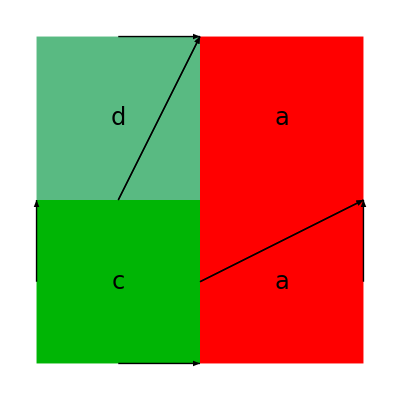

```mathematica
drawHomotopyEdgesOfTiles[{1,{0,0}}]
```

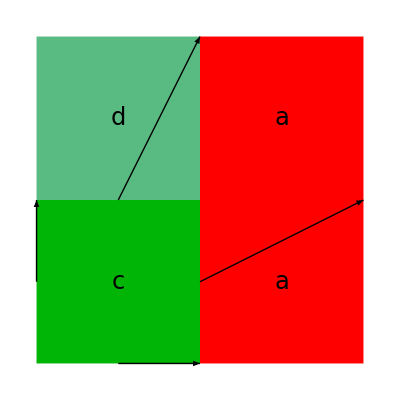
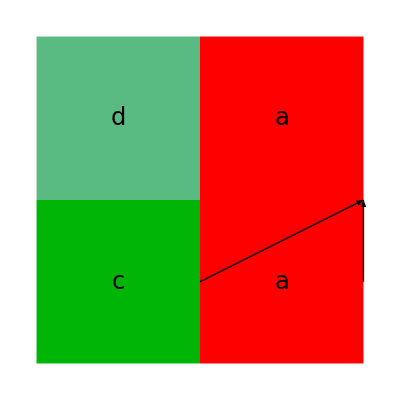
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[drawHomotopyEdgesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

```mathematica
Table[drawHomotopysEdges[i],{i,1,Length[sEdges]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawsEdges[1]
```

-Graphics-

```mathematica
homotopysEdges=ConstantArray[0,Length[sEdges]];
homotopysEdgesDirectionsIndices=ConstantArray[0,Length[sEdges]];


Clear[se,ps,es,locsH,xx,yy,ts,seNum]
For[seNum=1,seNum≤ Length[sEdges],seNum++,
se=sEdges⟦seNum⟧;
seHpreimage=Table[Position[HedgesSimple⟦se⟦i,1⟧⟧,se⟦i,2⟧],{i,1,Length[se]}];
{ps,es}=Transpose[se];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototilesMidEdges⟦ps⟦i⟧⟧⟦es⟦i⟧⟧},{i,1,Length[ps]}];
locsH=Table[Expand[FullSimplify[ComputeLocationsMidEdges[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
seHpreimageLocations=Table[Table[locsH⟦j⟧⟦seHpreimage⟦j⟧⟦i,1⟧,seHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[seHpreimage⟦j⟧]}],{j,1,Length[seHpreimage]}];
seHpreimageFlattened=Flatten[seHpreimage,1];
seHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[seHpreimage⟦i⟧]],{i,1,Length[seHpreimage]}],1];
hsedgesindices=Values[Normal[PositionIndex[Flatten[seHpreimageLocations,1]]]];
hsedgesDirectionsIndices=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Table[{yy⟦i⟧,xx⟦i⟧⟦1⟧,xx⟦i⟧⟦2⟧},{i,1,Length[xx]}],{j,1,Length[hsedgesindices]}];
homotopysEdgesDirectionsIndices[[seNum]]=hsedgesDirectionsIndices;

hsedges=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hsedgesindices]}];
homotopysEdges⟦seNum⟧=Table[Position[sEdges,hsedges⟦i⟧]⟦1,1⟧,{i,1,Length[hsedges]}];

]
homotopysEdges
```

{{5,1},{6,3},{3,5},{3,7},{3,1},{1,2},{1,4},{9,10},{8,10},{10,10},{20,17},{17,19},{17,18},{16,15},{15,15},{15,14},{13,17},{13,18},{12,18},{11,18}}

```mathematica
homotopysEdgesDirections=Table[
Table[
{hse,hsee}=homotopysEdgesDirectionsIndices⟦seNum⟧⟦i⟧;
If[
HverticesSimple⟦hse⟦1⟧,hse⟦2⟧,wPrototileAsprotoEdgesAsPosPairsOfVertices⟦hse⟦1⟧,hse⟦2⟧,hse⟦3⟧⟧⟦1⟧⟧
==
protoEdgesAsPosPairsOfVertices⟦hse⟦1⟧,HedgesSimple⟦hse⟦1⟧,hse⟦2⟧,hse⟦3⟧⟧⟧⟦1⟧,1,-1]

,{i,1,Length[homotopysEdgesDirectionsIndices⟦seNum⟧]}],{seNum,1,Length[homotopysEdgesDirectionsIndices]}];
homotopysEdgesDirections
```

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
sedgesHMtx=ConstantArray[0,{Length[sEdges],Length[sEdges]}];
Table[Table[sedgesHMtx⟦homotopysEdges⟦i⟧⟦j⟧⟧⟦i⟧+=homotopysEdgesDirections⟦i,j⟧,{j,1,Length[homotopysEdges⟦i⟧]}],{i,1,Length[homotopysEdges]}];
Print["W_E=",sedgesHMtx//MatrixForm]
```

W_E=(1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
mainHtile=Function[HedgesOfTile,Module[{found,tileNumber},
found=0;
Table[If[Sort[HedgesOfTile⟦i⟧]==Range[Length[HedgesOfTile⟦i⟧]],found++;tileNumber=i,0],{i,1,Length[HedgesOfTile]}];
If[found==1,tileNumber,Print["Error::mainHtile::HedgesOfTile found ",found," tiles (should be 1)"]]]];
HprototilesPos=Map[mainHtile,HedgesSimple]
Hprototiles=Table[wPrototileNumbers⟦i⟧⟦HprototilesPos⟦i⟧⟧,{i,1,Length[prototiles]}]
```

{1,1,1,1}

{3,2,1,4}

```mathematica
tilesHMtx=ConstantArray[0,{Length[prototiles],Length[prototiles]}];
Table[tilesHMtx⟦Hprototiles⟦i⟧⟧⟦i⟧+=1,{i,1,Length[Hprototiles]}];
tilesHMtx//MatrixForm
```

(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(*TEST Hprototiles*)
Table[{drawHomotopyVertices[i],drawProtoVertex[{Hprototiles⟦i⟧,1}]},{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}

```mathematica
drawDelta1=Function[seNum,Module[{sameDirTileNum,oppositeDirTileNum},
sameDirTileNum=Position[Transpose[δ1]⟦seNum⟧,1];
oppositeDirTileNum=Position[Transpose[δ1]⟦seNum⟧,-1];
Print["δ1(e_",seNum,")= p_",sameDirTileNum," - p_",oppositeDirTileNum];
If[Length[sameDirTileNum]≠ 0 && Length[oppositeDirTileNum]≠ 0,{drawsEdges[seNum],drawProtoVertex[{sameDirTileNum⟦1⟧⟦1⟧,1}],
drawProtoVertex[{oppositeDirTileNum⟦1⟧⟦1⟧,1}]}]]];
```

```mathematica
δ0=sEdgescVerticesMatrix
δ1=prototilessEdgesMatrix
Wv=cverticesHMtx
We=sedgesHMtx
Wf=tilesHMtx
```

{{1,1,0,1,1,-1,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,-1},{-1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,-1,0,0,0,1,1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,-1,0,1,1,1,0,0,0,0,0,0,0,0,-1,0,0,0},{0,-1,0,0,0,0,0,0,0,-1,0,0,1,1,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,1,1,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,1},{0,0,1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0},{1,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,1,0,0,1,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0},{-1,-1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,-1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,-1,0,0,0,1,1,0,1,1,0,0,0,-1,-1,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,1,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,1,1,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,1,0,0,0,1,0,0}}

{{1,-1,0,0,-1,0,0,-1,0,0,0,-1,-1,1,0,0,0,1,0,0},{-1,1,1,1,0,0,0,0,0,0,0,1,0,-1,0,-1,0,0,1,0},{0,0,-1,0,1,0,1,0,-1,0,0,0,1,0,0,1,-1,0,0,1},{0,0,0,-1,0,0,-1,1,1,0,0,0,0,0,0,0,1,-1,-1,-1}}

{{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{1,1,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,1,1,2,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1}}

{{1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}}

{{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}

```mathematica
δ1.δ0
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
We.δ0//MatrixForm
δ0.Wv//MatrixForm
```

(1 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | 0 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | -1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
1 | 1 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -2 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | -1 | -1 | 1
0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | -2 | -1 | -1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | -1 | 1 | 1 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | 0 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | -1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
1 | 1 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -2 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | -1 | -1 | 1
0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | -2 | -1 | -1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | -1 | 1 | 1 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
We.δ0==δ0.Wv
```

True

```mathematica
We.δ0-δ0.Wv//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Wf.δ1//MatrixForm
δ1.We//MatrixForm
Wf.δ1==δ1.We
```

(0 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 1
-1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0
1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1)

(0 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 1
-1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0
1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1)

True

```mathematica
AA=Table[A[i,j],{i,1,Length[prototiles]},{j,1,Length[prototiles]}];
BB=Flatten[AA.δ1-δ1.We];
eqs=Map[#==0&,BB];
sols=Solve[eqs,Flatten[AA]];
AA/.sols//MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

((A[1,1]
-1+A[1,1]
-1+A[1,1]
-1+A[1,1]) | (A[2,1]
A[2,1]
1+A[2,1]
A[2,1]) | (A[3,1]
1+A[3,1]
A[3,1]
A[3,1]) | (A[4,1]
A[4,1]
A[4,1]
1+A[4,1]))